a=[]
a.append(2)
for i in range(0,10):
    t=a[i]
    a.append((t+(2/t))/2)
print(a)

[2, 1.5, 1.4166666666666665, 1.4142156862745097, 1.4142135623746899, 1.414213562373095, 1.414213562373095, 1.414213562373095, 1.414213562373095, 1.414213562373095, 1.414213562373095]

```mathematica
RSolve[{2f[n]f[n+1]==f[n]^2+3,f[0]==2},f[n],n]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{f[n]→√3 Coth[2^n ArcCoth[2/(√3)]]}}

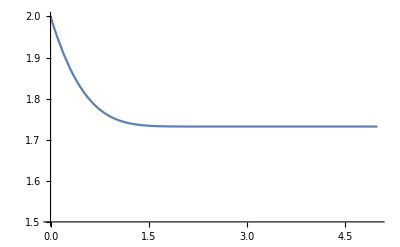

```mathematica
Plot[√3 Coth[2^n ArcCoth[2/(√3)]],{n,0,5},PlotRange->{1.5,2}]
```